```mathematica
filePath="/Users/dylan/thesis/pres_figs/";
blankBox[x_,y_,colour_]:={EdgeForm[Thin],colour,Rectangle[{x,y}]};
```

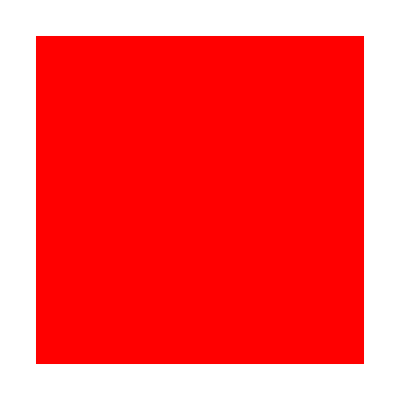

/Users/dylan/thesis/pres_figs/64x64_red.png

```mathematica
all = {};
For[i=0, i < 64, i++,
For[j=0,j<64,j++,
all = Append[all,blankBox[i,j,Red]]
]
]
Graphics[all]
Export[filePath<>"64x64_red.png",Graphics[all]]
```

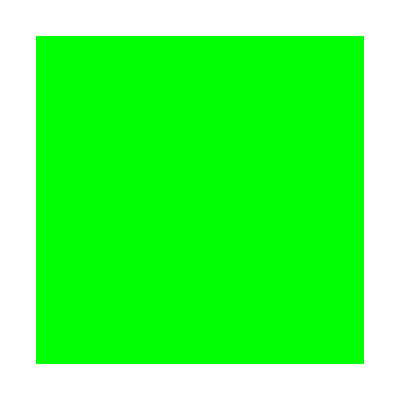

/Users/dylan/thesis/pres_figs/64x64_green.png

```mathematica
all = {};
For[i=0, i < 64, i++,
For[j=0,j<64,j++,
all = Append[all,blankBox[i,j,Green]]
]
]
Graphics[all]
Export[filePath<>"64x64_green.png",Graphics[all]]
```

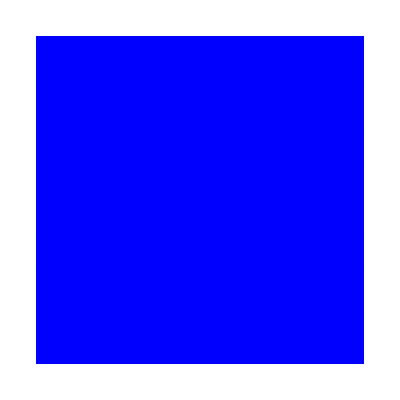

/Users/dylan/thesis/pres_figs/64x64_blue.png

```mathematica
all = {};
For[i=0, i < 64, i++,
For[j=0,j<64,j++,
all = Append[all,blankBox[i,j,Blue]]
]
]
Graphics[all]
Export[filePath<>"64x64_blue.png",Graphics[all]]
```

```mathematica
all = {};
For[i=0, i < 32, i++,
For[j=0,j<32,j++,
all = Append[all,blankBox[i,j,Red]]
]
]
Graphics[all]
Export[filePath<>"32x32_red.png",Graphics[all]]
```